```mathematica
NotebookEvaluate["definitions.nb"]
```

## Network functions

Run the rate-based neural network for nSteps, recording every recNSteps

```mathematica
ClearAll@RateModel;RateModel[M_?(MatrixQ[#,NumberQ]&),h0_?(VectorQ[#,NumberQ]&),nSteps_?NumericQ,recNSteps_?NumericQ,dt_?NumericQ,ϕ_:Tanh,useTQDM_:True]:=With[{J=(1-IdentityMatrix[Length@M])M},Module[{h=h0,cell=If[useTQDM,PrintTemporary@Dynamic@iRateModel],result},result=Table[Do[h+=(-h+J.ϕ[h])dt,recNSteps];h,{iRateModel,Floor[nSteps/recNSteps]}];If[useTQDM,NotebookDelete@cell];result]]
```

```mathematica
M[α_,n_]:=RandomVariate[StableDistribution[α,0,0,(2n)^(-1/α)],{n,n}]
```

```mathematica
IPR[ψ_,q_]:=Total[#^(2q)]/(Total[#^2])^q&@Abs[ψ]
```

## Network simulation

```mathematica
(localfields=Table[BlockRandom[With[{n=2000,g=1.75},With[{mat=g M[α,n]},RateModel[mat,RandomReal[{-1,1},n],10^5,10^2,10^-3,Tanh]]],RandomSeeding->1],{α,{1.2,2}}])//ByteCount@#/2.^20&
```

31.4793

Activity trace (cf. Landau Sompolinsky PLOS) with “activity speed”

```mathematica
Table[ArrayPlot[{Range[2]},ColorFunction->ColorData[i],ColorFunctionScaling->False,AspectRatio->.3,PlotLabel->i,ImageSize->50],{i,113}]
```

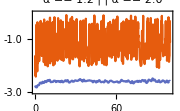

```mathematica
Table[Tanh@localfields[[alphai]]//Differences//Map[Log10@IPR[#,2]&],{alphai,2}]//ListLinePlot[#,PlotStyle->ColorData[108],Evaluate@FigureStyle@pubStyle[Medium],Frame->{True,True,False,False},ImagePadding->{{50,10},{50,10}},PlotRange->{{Full,Full},{-3,0}},FrameTicks->linearFrameTicks,FrameLabel->{ShiftFrameLabel[15]@"Time",ShiftFrameLabel[-5]@"Log_10(IPR_2)"},DataRange->{0,100},ImageSize->Small,PlotLabel->TextGrid@{{Style["α == 1.2",pubStyle[16],.75#&/@ColorData[108,1]],"",Style["α == 2.0",pubStyle[16],.75#&/@ColorData[108,2]]}}]&
```

```mathematica
Export["fig/IPR.pdf",ResourceFunction["EvaluatePreviousCell"][]]
```

fig/IPR.pdf

```mathematica
With[{data=Tanh@localfields[[1]]//Differences//Abs},Rasterize@ListLinePlot[#[[;;600]],PlotStyle->ColorData[108],Evaluate@FigureStyle@pubStyle[Medium],FrameTicks->{{0,200,400,600},Automatic},Frame->{True,True,False,False},PlotRange->{0,.4},FrameLabel->{ShiftFrameLabel[15]@"Site",ShiftFrameLabel[-5]@"Magnitude"},ImageSize->Small,PlotRangeClipping->False]&/@data[[-200;;;;1]]]//ListAnimate
```

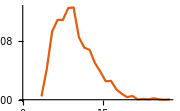

```mathematica
With[{data=Tanh@localfields[[1]]//Differences//Abs},ListLinePlot[HistogramPDFList@Total@data,PlotStyle->ColorData[108],Evaluate@FigureStyle@pubStyle[Medium],ImageSize->Small]]
```

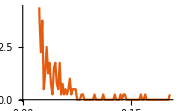

```mathematica
With[{data=Tanh@localfields[[1]]//Differences//Abs},ListLinePlot[HistogramPDFList@data[[-1]],PlotStyle->ColorData[108],Evaluate@FigureStyle@pubStyle[Medium],ImageSize->Small]]
```

```mathematica
With[{data=Tanh@localfields[[1]]//Differences//Abs},ListLinePlot[Total@data,PlotStyle->ColorData[108],Evaluate@FigureStyle@pubStyle[Medium],ImageSize->Small]]
```

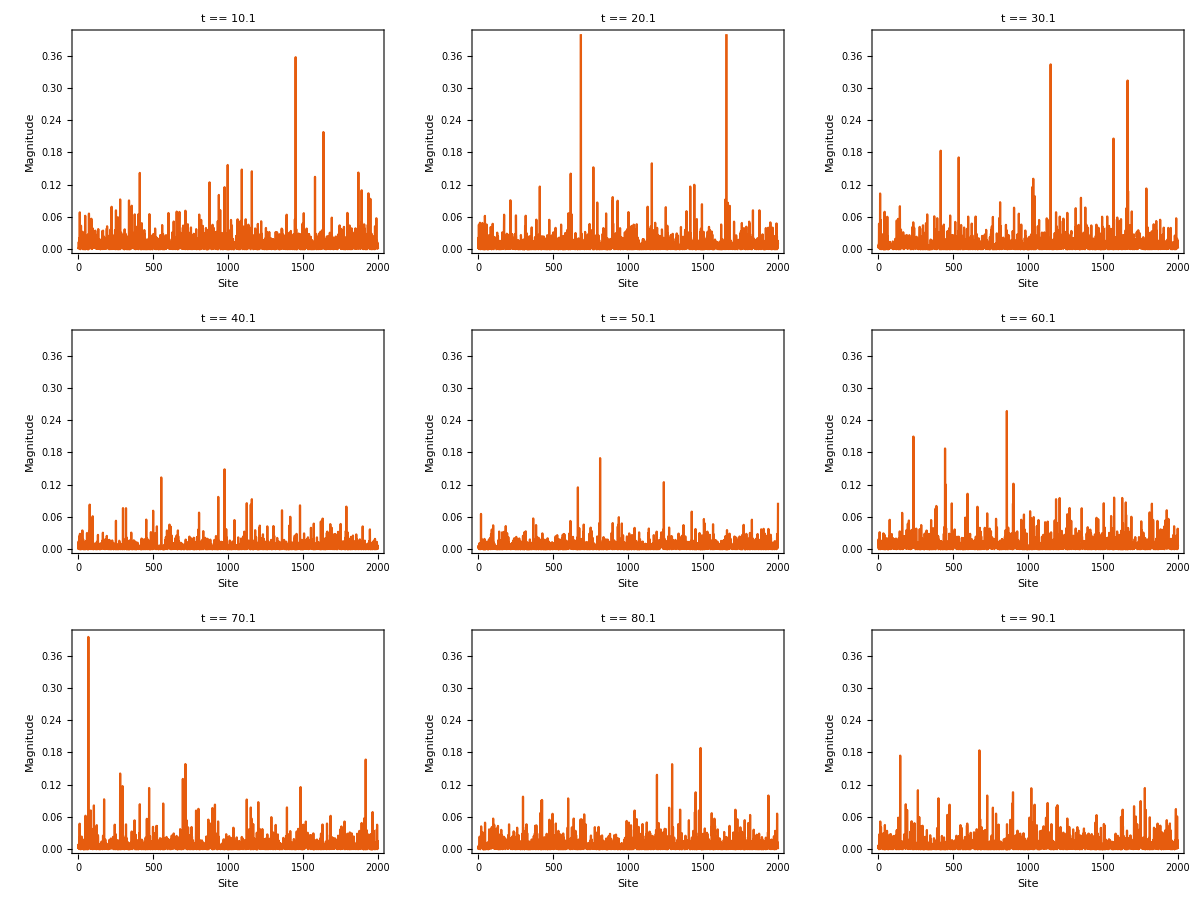

```mathematica
With[{data=Tanh@localfields[[1]]//Differences//Abs},Table[ListLinePlot[data[[t]],PlotStyle->ColorData[108],Evaluate@FigureStyle@pubStyle[Medium],Frame->{True,True,False,False},PlotRange->{0,.4},FrameLabel->{ShiftFrameLabel[15]@"Site",ShiftFrameLabel[-5]@"Magnitude"},ImageSize->Small,PlotRangeClipping->False,PlotLabel->Style[StringTemplate["t == ``"][t/10],pubStyle[16]]],{t,Range[101,Length@data,100]}]]//Partition[#,3]&//Grid
```

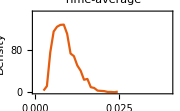

```mathematica
With[{data=Tanh@localfields[[1]]//Differences//Abs},ListLinePlot[HistogramPDFList@(Total[#]/Length[#]&)@data[[-900;;]],PlotStyle->ColorData[108],Evaluate@FigureStyle@pubStyle[Medium],Frame->{True,True,False,False},PlotRange->{{0,.04},{0,150}},FrameLabel->{ShiftFrameLabel[15]@"Magnitude",ShiftFrameLabel[-5]@"Density"},ImageSize->Small,PlotRangeClipping->False,PlotLabel->Style["Time-average",pubStyle[16]]]]
```

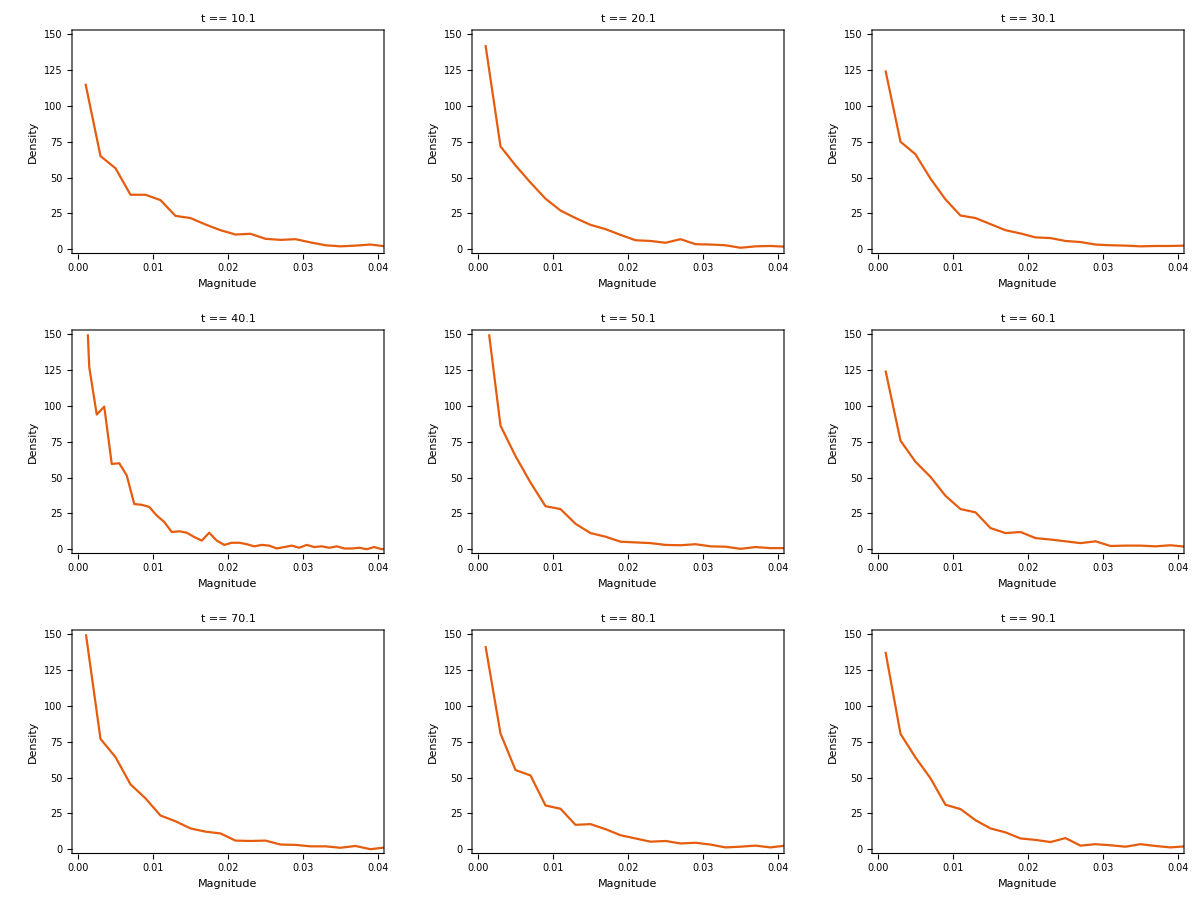

```mathematica
With[{data=Tanh@localfields[[1]]//Differences//Abs},Table[ListLinePlot[HistogramPDFList@data[[t]],PlotStyle->ColorData[108],Evaluate@FigureStyle@pubStyle[Medium],Frame->{True,True,False,False},PlotRange->{{0,.04},{0,150}},FrameLabel->{ShiftFrameLabel[15]@"Magnitude",ShiftFrameLabel[-5]@"Density"},ImageSize->Small,PlotRangeClipping->False,PlotLabel->Style[StringTemplate["t == ``"][t/10],pubStyle[16]]],{t,Range[101,Length@data,100]}]]//Partition[#,3]&//Grid
```

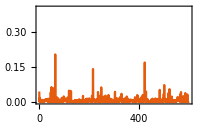

```mathematica
Tanh@localfields[[1]]//Differences//Last//Abs//Show[ListLinePlot[Table[{i,#[[i]]},{i,1,600}],PlotStyle->ColorData[108],Evaluate@FigureStyle@pubStyle[Medium],FrameTicks->{{0,200,400,600},Automatic},Frame->{True,True,False,False},ImagePadding->{{50,10},{50,10}},PlotRange->{0,.4},FrameLabel->{ShiftFrameLabel[15]@"Site",ShiftFrameLabel[-5]@"Magnitude"},ImageSize->Small,PlotRangeClipping->False],Graphics@Inset[ListLinePlot[Table[{i,#[[i]]},{i,0,100}],PlotStyle->ColorData[108],Evaluate@FigureStyle@pubStyle[Small],PlotRange->{0,.2},AspectRatio->.5],Scaled@{1,1},Scaled@{1,.5},Scaled@.9],ImagePadding->40,ImageSize->200]&
```

```mathematica
Export["fig/sites_alpha_120.pdf",ResourceFunction["EvaluatePreviousCell"][]]
```

fig/sites_alpha_120.pdf

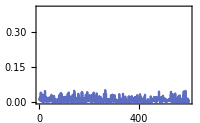

```mathematica
Tanh@localfields[[2]]//Differences//Last//Abs//Show[ListLinePlot[Table[{i,#[[i]]},{i,1,600}],PlotStyle->ColorData[108,2],Evaluate@FigureStyle@pubStyle[Medium],FrameTicks->{{0,200,400,600},Automatic},Frame->{True,True,False,False},ImagePadding->{{50,10},{50,10}},PlotRange->{0,.4},FrameLabel->{ShiftFrameLabel[15]@"Site",ShiftFrameLabel[-5]@"Magnitude"},ImageSize->Small,PlotRangeClipping->False],Graphics@Inset[ListLinePlot[Table[{i,#[[i]]},{i,0,100}],PlotStyle->ColorData[108,2],Evaluate@FigureStyle@pubStyle[Small],PlotRange->{0,.2},AspectRatio->.5],Scaled@{1,1},Scaled@{1,.5},Scaled@.9],ImagePadding->40,ImageSize->200]&
```

```mathematica
Export["fig/sites_alpha_200.pdf",ResourceFunction["EvaluatePreviousCell"][]]
```

fig/sites_alpha_200.pdf

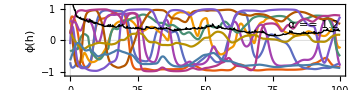

```mathematica
With[{alphai=1},Show[RandomSample[Transpose@Tanh@localfields[[alphai,;;,;;]],10]//ListLinePlot[#,ImageSize->Medium,PlotRange->{{Full,Full},1.1{-1,1}},PlotTheme->"Scientific",FrameStyle->pubStyle[],AspectRatio->1/4,FrameLabel->{"Time","ϕ(h)"}(*PlotLabel->StringTemplate["α == ``"]@{1.2,2.0}[[alphai]]*),LabelStyle->pubStyle[],DataRange->{0,100}]&,ListLinePlot[Map[50#&@*Mean@*Abs]@Differences[Tanh@localfields[[alphai]]],PlotStyle->{Thick,Black},DataRange->{0,100},PlotRange->All],Graphics@Inset[Framed[Style["α == 1.2",pubStyle[]],Background->Opacity[.85,White]],{90,.5}]]]
```

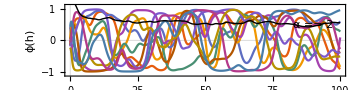

```mathematica
With[{alphai=2},Show[RandomSample[Transpose@Tanh@localfields[[alphai,;;,;;]],10]//ListLinePlot[#,ImageSize->Medium,PlotRange->{{Full,Full},1.1{-1,1}},PlotTheme->"Scientific",FrameStyle->pubStyle[],AspectRatio->1/4,FrameLabel->{"Time","ϕ(h)"}(*PlotLabel->StringTemplate["α == ``"]@{1.2,2.0}[[alphai]]*),LabelStyle->pubStyle[],DataRange->{0,100}]&,ListLinePlot[Map[50#&@*Mean@*Abs]@Differences[Tanh@localfields[[alphai]]],PlotStyle->{Thick,Black},DataRange->{0,100},PlotRange->All],Graphics@Inset[Framed[Style["α == 2",pubStyle[]],Background->Opacity[.85,White]],{90,.5}]]]
```

2-IPR of the activity velocity vector over neurons indicates multifractality

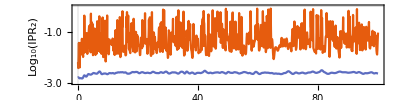

```mathematica
Table[Tanh@localfields[[alphai]]//Differences//Map[Log10@IPR[#,2]&],{alphai,2}]//ListLinePlot[#,PlotRange->{{Full,Full},{-3,0}},PlotTheme->"Scientific",FrameStyle->pubStyle[],FrameTicks->linearFrameTicks,AspectRatio->1/4,FrameLabel->{"Time","Log_10(IPR_2)"},DataRange->{0,100},FrameTicks->linearFrameTicks]&
```

```mathematica
ResourceFunction["EvaluatePreviousCell"]/@{6,4,1}//Map@List//ResourceFunction["PlotGrid"]
```

-Graphics-

```mathematica
ResourceFunction["EvaluatePreviousCell"][]//Export["/import/silo5/wardak/levy_matrices/figures/correlations.pdf",#]&
```

/import/silo5/wardak/levy_matrices/figures/correlations.pdf

D_q plot averaged over t confirms multifractality

```mathematica
LaunchKernels[19]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local],KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local],KernelObject[17,local],KernelObject[18,local],KernelObject[19,local]}

```mathematica
With[{n=2000,dq=.01},ParallelOuter[{alphai,q}↦{q,With[{diffs=Differences[Tanh@localfields[[alphai]]]},Table[Log[n,IPR[diffs[[t]],q]]/(1-q),{t,1,999,50}]]},Range[2],Rest@Most@Range[0,1,dq]~Join~Rest@Range[1,2,dq]]//BinarySerialize]
```

ByteArray[…]

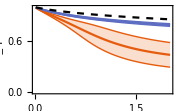

```mathematica
With[{n=2000},BinaryDeserialize[ResourceFunction["EvaluatePreviousCell"][]]//Show[ListLinePlot[Map[MapAt[Around[Mean[#],StandardDeviation[#]]&,2],#,{2}],IntervalMarkers->"Bands",PlotRange->{0,1},Frame->{True,True,False,False},FrameLabel->{ShiftFrameLabel[15]@"q",ShiftFrameLabel[-5]@"D_q"},ImageSize->Small(*,LabelStyle->pubStyle[Small],PlotLegends->Placed[StringTemplate["α == ``"]/@({120,200}/100.),Scaled@{.275,.225}]*),PlotStyle->ColorData[108],Evaluate@FigureStyle@pubStyle[Medium],ImagePadding->{{50,10},{50,10}}],ListLinePlot[With[{gaussianVector=RandomVariate[NormalDistribution[],n]},Table[{q,Log[n,IPR[gaussianVector,q]]/(1-q)},{q,Rest@Most@Range[0,1,.01]~Join~Rest@Range[1,2,.01]}]],PlotStyle->{Dashed,Black}]]&]
```

```mathematica
Export["fig/D_q.pdf",ResourceFunction["EvaluatePreviousCell"][]/.{Unevaluated->Identity}]
```

fig/D_q.pdf

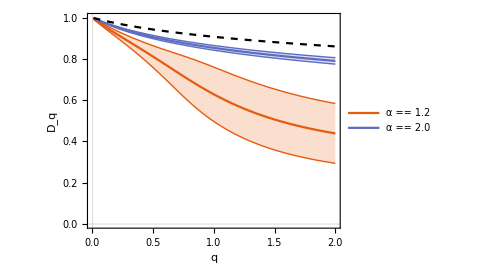

```mathematica
With[{n=2000},BinaryDeserialize[ResourceFunction["EvaluatePreviousCell"][]]//Show[ListLinePlot[Map[MapAt[Around[Mean[#],StandardDeviation[#]]&,2],#,{2}],IntervalMarkers->"Bands",PlotRange->{0,1},PlotTheme->"Scientific",FrameStyle->pubStyle[],AspectRatio->3/4,FrameLabel->{"q","D_q"},ImageSize->Medium,LabelStyle->pubStyle[],PlotLegends->Placed[StringTemplate["α == ``"]/@({120,200}/100.),Scaled@{.2,.4}]],ListLinePlot[With[{gaussianVector=RandomVariate[NormalDistribution[],n]},Table[{q,Log[n,IPR[gaussianVector,q]]/(1-q)},{q,Rest@Most@Range[0,1,.01]~Join~Rest@Range[1,2,.01]}]],PlotStyle->{Dashed,Black}]]&]
```